# Impedância Série de Linhas de Transmissão

## Prof. Antonio Carlos Siqueira de Lima

### Opções de programa

```mathematica
Off[General::"spell",General::"spell1"];
```

```mathematica
SetOptions[{Plot,LogLinearPlot,LogLogPlot},Axes->False,Frame->True,ImageSize->450,PlotStyle->{AbsoluteThickness[2]},BaseStyle->{14,FontFamily->"Helvetica"}];
```

## Impedância Interna

A impedância interna da linha de transmissão apresenta o comportamento variante com a freqüência devido ao efeito pelicular.

### Condutores sólidos

```mathematica
r1=2.5951/2 10^-2;
 r0=(1/2 -0.3565)2.5951 10^-2;
 r1pr=1.10490/2 10^-2;
```

```mathematica
ρ0c=0.03206*(10^(-3)) * π* (r1^2-r0^2)
```

1.55607×10^-8

```mathematica
T=75;
κ=.750223;
α=0.00454562;
ρc=ρ0c (1+α T)/κ
```

2.78127×10^-8

Parâmetros dos cabos pára-raios por metro

```mathematica
ρ0pr= π  *2.8645* (10^-3)*r1pr^2;
Tpr=25;
κpr=0.778767;
ρpr=ρ0pr  (1+α Tpr)/κpr
```

3.92755×10^-7

```mathematica
z1in(ω_,μ_:(4 π)/10^7):=(√((ⅈ ω μ)/ρc) ρc)/(2 π r1)(Subscript[I, 0](√((ⅈ ω μ)/ρc) r1))/(Subscript[I, 1](√((ⅈ ω μ)/ρc) r1))
```

```mathematica
z2in(ω_,μ_:(4 π)/10^7):=(√((ⅈ ω μ)/ρc) ρc)/(2 π r1)(Subscript[I, 0](√((ⅈ ω μ)/ρc) r1) Subscript[K, 1](√((ⅈ ω μ)/ρc) r0)+Subscript[I, 1](√((ⅈ ω μ)/ρc) r0) Subscript[K, 1](√((ⅈ ω μ)/ρc) r1))/(Subscript[I, 1](√((ⅈ ω μ)/ρc) r1) Subscript[K, 1](√((ⅈ ω μ)/ρc) r0)-Subscript[I, 1](√((ⅈ ω μ)/ρc) r0) Subscript[K, 1](√((ⅈ ω μ)/ρc) r1))
```

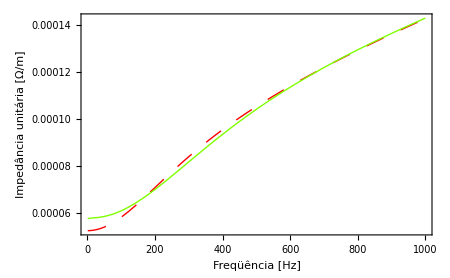

```mathematica
Plot[{Re[z1in[2 π f]],Re[z2in[2 π f]]},{f,1,1000},PlotStyle->{{Hue[0],Dashing[{0.03}]},Hue[0.25]},FrameLabel->{"Freqüência [Hz]","Impedância unitária [Ω/m]"},PlotRange->All]
```

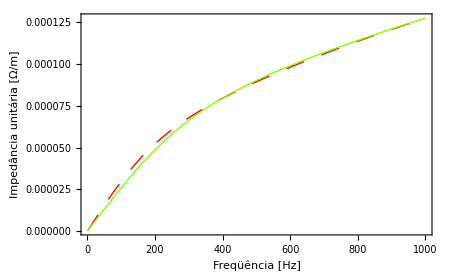

```mathematica
Plot[{Im[z1in[2 π f]],Im[z2in[2 π f]]},{f,1,1000},PlotStyle->{{Hue[0],Dashing[{0.03}]},Hue[0.25]},FrameLabel->{"Freqüência [Hz]","Impedância unitária [Ω/m]"},PlotRange->All]
```

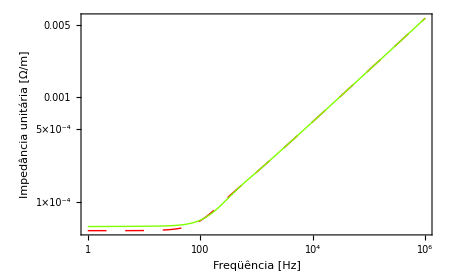

```mathematica
LogLogPlot[{Abs[z1in[2 π f]],Abs[z2in[2 π f]]},{f,1,10^6},PlotStyle->{{Hue[0],Dashing[{0.03}]},Hue[0.25]},FrameLabel->{"Freqüência [Hz]","Impedância unitária [Ω/m]"},PlotRange->All,PlotPoints->500]
```

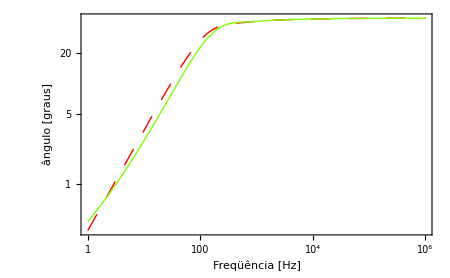

```mathematica
LogLogPlot[{Arg[z1in[2 π f]]/°,Arg[z2in[2 π f]]/°},{f,1,10^6},PlotStyle->{{Hue[0],Dashing[{0.03}]},Hue[0.25]},FrameLabel->{"Freqüência [Hz]","ângulo [graus]"},PlotRange->All,PlotPoints->500]
```

## Impedância Externa

Para o caso da impedância externa considera-se apenas um condutor monofásico situado a10m de altura do solo e com alura constante.

```mathematica
Ze(ω_,ρs_: 100.0,μ_:(4 π)/10^7):=(ⅈ ω μ)/(2 π)log((2 (√(ρs/(ⅈ ω μ))+10))/r1)
```

```mathematica
Zsolo(f_,ρs_:100.0,μ_:(4 π)/10^7):=(9.869 f)/10^7+ⅈ  f μ log((658.4 √(ρs/f))/r1)+ⅈ  f μ log(20.0/r1)
```

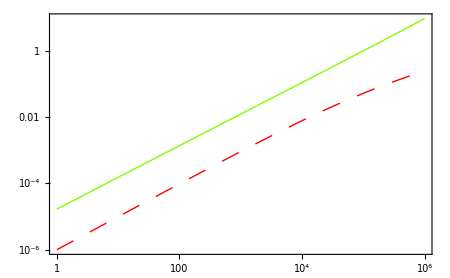

```mathematica
LogLogPlot[{Re[Ze[2 π f]],Im[Ze[2 π f]]},{f,1,10^6},PlotStyle->{{Hue[0],Dashing[{0.03}]},Hue[0.25]},PlotRange->All,PlotPoints->500]
```

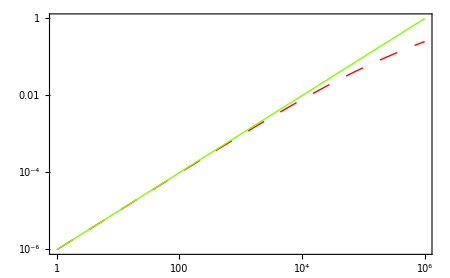

```mathematica
LogLogPlot[{Re[Ze[2 π f]],Re[Zsolo[f]]},{f,1,10^6},PlotStyle->{{Hue[0],Dashing[{0.03}]},Hue[0.25]},PlotRange->All,PlotPoints->500]
```

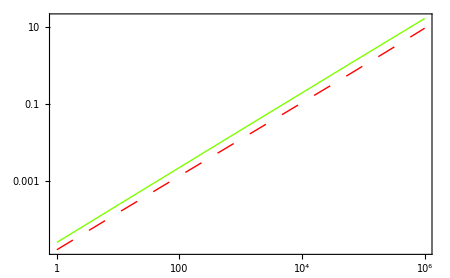

```mathematica
LogLogPlot[{Im[Ze[2 π f]],Im[Zsolo[f]]},{f,1,10^6},PlotStyle->{{Hue[0],Dashing[{0.03}]},Hue[0.25]},PlotRange->All,PlotPoints->500]
```